# Introduction to Public Key Encryption

## Private key ciphers

In order to secure private communication, cryptographic ciphers have been around for thousands of years. One of the more famous ones was used by Julius Caesar and is called the Caesar Cipher. It involves the substitution of the letters of the alphabet by that same alphabet but shifted. Below is an example.

```mathematica
(* Consider the letters of the alphabet (lower case) *)
alphabet=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Now we construct a shifted alphabet

```mathematica
shiftedalphabet=RotateLeft[alphabet,3]
```

{d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,a,b,c}

The cipher is the algorithm that tells us how the two are related, i.e.

```mathematica
cipher=Thread[alphabet->shiftedalphabet]
```

{a→d,b→e,c→f,d→g,e→h,f→i,g→j,h→k,i→l,j→m,k→n,l→o,m→p,n→q,o→r,p→s,q→t,r→u,s→v,t→w,u→x,v→y,w→z,x→a,y→b,z→c}

This list, here called a cipher, tells us how each letter of the alphabet is substituted. So if we  construct a message written in the original alphabet, the Caesar Cipher substitutes each letter according to the rule "cipher".

```mathematica
ceasar[inputstring_]:=StringReplace[inputstring,cipher]
```

```mathematica
julius=ceasar["You blocks,you stones,you worse than senseless things!
O you hard hearts,you cruel men of Rome, knew you not Pompey?"]
```

Yrx eorfnv,brx vwrqhv,brx zruvh wkdq vhqvhohvv wklqjv!
O brx kdug khduwv,brx fuxho phq ri Rrph, nqhz brx qrw Prpshb?

So the list "julius" now contains the encrypted message, but how does the recipient know how to decipher it? They need an algorithm, or cipher, to decode the message. That is, someone must tell the recipients beforehand what the cipher is, and such a system is called a private key system. Here the "key" is the algorithm for encryption. Knowing that private key, we can undo this message.

```mathematica
uncipher=Thread[shiftedalphabet->alphabet]
```

{d→a,e→b,f→c,g→d,h→e,i→f,j→g,k→h,l→i,m→j,n→k,o→l,p→m,q→n,r→o,s→p,t→q,u→r,v→s,w→t,x→u,y→v,z→w,a→x,b→y,c→z}

```mathematica
StringReplace[julius,uncipher]
```

You blocks,you stones,you worse than senseless things!
O you hard hearts,you cruel men of Rome, knew you not Pompey?

Private key crypto-systems have some obvious pitfalls, this is called the key distribution problem

Requires direct communication between user and sender of key, and is compromised by eavesdropping, etc.

Substitution keys are very easy to decrypt even without the key (e.g. Mary Queen of Scots).

```mathematica
ClearAll["Global`*"]
```

## Public key (RSA) encryption

Rivest, Shamir, Adleman

Alice and Bob want to communicate in a secure manner. Instead of sending Bob a private key (which can be compromised) she follows this protocol

She chooses two prime numbers p and q, so that p≠q. (A prime number can only be factored into itself and 1)

She computes the modulus n = p q. A number that is a product of two primes is called semi-prime, so n is semi-prime.

She computes the totient  ϕ = (p-1)(q-1).

She chooses the public-key exponent, e, an arbitrary number. It must satisfy  1  < e <  ϕ.   But e, ϕ are not allowed to have common factors (co-prime).

She chooses a number d (the private key) so that  d e = 1 Mod[ϕ]  (Note: d should be an integer if it isn’t try another value for e)

After Alice completes this checklist she publishes her public-key which is simply the pair (n,e). But she keeps q, ϕ, d  private.

Now Bob wants to send Alice a secure message.  He goes on the internet and finds her public key (n,e) which she published for all to see. Let’s say Bob has a string of characters M="wassup" that he wants to send. He converts that string into an integer, he does this through the means of a conversion function N=f(M).  Given the string of characters M and the function f, the latter maps M into an integer N. It is important that f is invertible, i.e. given N we can apply f^-1(N)  to get a unique M.

Having constructed N, Bob looks at the public key  e, n  and constructs

C = N^e Mod n

The number C is the cipher, and he sends that number to Alice, (By the way, others are also listening and were able to get Bob's number C). 

Alice simply takes her private key (not shared by anyone!) and evaluates

C^d  Mod n

she claims that this is equal to N and she uses Bob's public table for  f^-1 to find the original message M.

Why does this work ?

#### Some results from number theory: -Graphics- Theorem I: Fermat's Little Theorem

Let p be  a prime number, then

a^(p-1) Mod p = 0  if  p divides a

a^(p-1) Mod p = 1  if  p does not divide a

Examples:

```mathematica
fermat[a_,p_]:=Mod[a^(p-1),p]
```

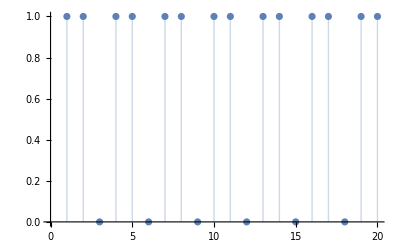

```mathematica
Table[fermat[a,3],{a,1,20}];
ListPlot[%,Filling->Axis]
```

#### Theorem II:

p ≠ q  are prime numbers and

if   x = a Mod p and  x = a Mod q   then  x = a Mod p q


Proof:  Since x = a Mod p this implies that  x = a + K p  where K is an integer
            Since x = a Mod q   "       "        "      x = a + L q     "       L      "
            
            therefore 0 = K p - L q  but  since  p,q are prime K = M q and L = M p where M is some integer.
            Now, since x = a + L q = a + M p q, which implies that
            x = a Mod p q     QED

#### Theorem III:

Modular arithmetic allows the following identity

(x y) Mod n  = (x Mod n) (y Mod n)  Mod n

Lets take a few examples.

```mathematica
x=5;
y=7;
n=3;
```

```mathematica
Mod[x y,n]
Mod[x,n]
Mod[y,n]
Mod[x y,n]==Mod[Mod[x,n] Mod[y,n],n]
```

2

2

1

True

Using these theorems we take Bob's value C = N^e Mod n;   Alice then creates 

C^d Mod n  = (  N^e Mod n  N^e Mod n ... N^e Mod n )  Mod n  =  N^ed  Mod n.  Let us first evaluate

N^(e d) Mod p = N^(1 + k (p-1)(q-1)) Mod p    

Why ?  Remember, Alice chose de = 1 Mod ϕ = 1 Mod (p-1)(q-1) which implies
that  de = 1 + k (p-1)(q-1)  where k is an integer. 

Therefore

N^(e d) Mod p = N [ N^(k(q-1))]^(p-1) Mod p = ( N Mod p) (  [ N^(k(q-1))]^(p-1) Mod p)  Mod p

Now lets use Theorem I  to state that

[N^(k(q-1))]^(p-1)  Mod p = 0  if p divides N
[N^(k(q-1))]^(p-1) Mod p = 1  if p does not divide N

so in Case I,  N^ed Mod p = 0 Mod p  
                      but  0 = N Mod p  therefore
                     N^ed Mod p = N Mod p

in case II  

N^(e d) Mod p =  ( N Mod p ) Mod p =  N Mod p  so in either case we have

N^(e d) Mod p = N Mod p

Since we proved the above for p, we can do the same to show that

N^(e d) Mod q = N Mod q

We now use Theorem II  to equate

N^ed Mod p q = N Mod p = N Mod q  or

N^ed Mod n =  N Mod n, but if  N < n  this is the same as
N^ed Mod n =  N    QED

Thus Alice can re-constitute the value N Mod n, which is Bob's original message (which can then be transcribed using his function f^-1)

Let's look at a specific example. First Alice produces her public key as described above.

```mathematica
(* Alice chooses 2 prime numbers, p, q that are not co-prime *)
```

```mathematica
p=23;
q=11;
```

```mathematica
(* she constructs the modulus *)
n=p q
```

253

```mathematica
(* then the totient *)
ϕ = (p-1)(q-1)
```

220

```mathematica
(* choose e, it cannot have a common factor with ϕ *)
e=31;
?GCD
GCD[ϕ,e]
```

RowBox[{"GCD", "[", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives the greatest common divisor of the SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]].

1

```mathematica
(* Alice constructs her private exponent d which is a solution of the equation  e d = 1 Mod[ϕ] *)
(* Mathematiac has a routine that lets you solve the above equation for d, the Modular inverse of e *)
?PowerMod
```

RowBox[{"PowerMod", "[", RowBox[{StyleBox["a", "TI"], ",", StyleBox["b", "TI"], ",", StyleBox["m", "TI"]}], "]"}] gives RowBox[{SuperscriptBox[StyleBox["a", "TI"], StyleBox["b", "TI"]], " ", "mod", " ", StyleBox["m", "TI"]}]. 
RowBox[{"PowerMod", "[", RowBox[{StyleBox["a", "TI"], ",", RowBox[{"-", "1"}], ",", StyleBox["m", "TI"]}], "]"}] finds the modular inverse of StyleBox["a", "TI"] modulo StyleBox["m", "TI"].
RowBox[{"PowerMod", "[", RowBox[{StyleBox["a", "TI"], ",", RowBox[{"1", "/", StyleBox["r", "TI"]}], ",", StyleBox["m", "TI"]}], "]"}] finds a modular StyleBox["r", "TI"]SuperscriptBox["", "th"] root of StyleBox["a", "TI"].

```mathematica
d=PowerMod[e,-1,ϕ]
```

71

```mathematica
(* Alice now publishes her public key *)

key={n,e}
```

{253,31}

```mathematica
(* Bob uploads Alice's key he then wants to send the number N = 199 to Alice encrypted *)
```

```mathematica
Bobsmessage=199;
Bobsmessage^e
Cnum=Mod[%,n]
```

183842267821883126536849737740850968039082927251300875492337211941406199

221

```mathematica
(* So Alice, as well eavesdroppers, have access to this number *)
(* But Alice uses her exponent d to construct N *)

Cnum^d
Alicesmessage=Mod[%,n]
```

28304235669297588721788477479545341778914861566574429012673694928037843063383655685607970807954357099304258267447549532586798529180583570518440104230395480098437129621

199

Thus Alice easily obtains Bob's original message,

```mathematica
Bobsmessage
Alicesmessage
```

199

199

However the eavesdroppers are hard at work. They know the public key n,e, and all they need to do is factor n it in order to get p,q as well as the totient. With the totient they can easily solve the equation

d e = 1 Mod ϕ

for exponent d (the Modular inverse of e ).  With knowledge of the totient, the eavesdroppers employ Alice’s algorithm in order to find N.  So why is this encryption scheme secure?

Answer: It is  difficult to factor a number n if it is very large. Indeed, as the number of digits in n increase, known classical algorithms require computer resources (e.g. time, memory) that scale as a power of n. At a certain point, for very large n, available technology is not able to perform the required task. Therefore, ensuring the security of an encrypted message.

#### Examples:

```mathematica
?FactorInteger
```

RowBox[{"FactorInteger", "[", StyleBox["n", "TI"], "]"}] gives a list of the prime factors of the integer StyleBox["n", "TI"], together with their exponents. 
RowBox[{"FactorInteger", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"]}], "]"}] does partial factorization, pulling out at most StyleBox["k", "TI"] distinct factors.

```mathematica
?Timing
```

RowBox[{"Timing", "[", StyleBox["expr", "TI"], "]"}] evaluates StyleBox["expr", "TI"], and returns a list of the time in seconds used, together with the result obtained.

```mathematica
Timing[FactorInteger[15]]
```

{0.000033,{{3,1},{5,1}}}

```mathematica
Timing[FactorInteger[1698532224795]]
```

{0.000036,{{3,2},{5,1},{7,2},{23,1},{33491713,1}}}

```mathematica
Timing[FactorInteger[745237738484848484858585858820303836464646464646698532224795]]
```

{0.480108,{{5,1},{43,1},{73,1},{109919,1},{19736531,1},{23064124095515717,1},{948971049172828259916128437,1}}}

Note the time resources required by Mathematica as the number to be factored grows in size.